## 1. Imports and Definitions

We need to import finite elements directly to have access to some functions

```mathematica
<<NDSolve`FEM`
```

The greatest function ever created, reference cell block directly above

```mathematica
«:=Out[
ToExpression[
StringCases[
ToString[PreviousCell[CellStyle->"Output"]//NotebookRead//Last],
"Out["~~d:DigitCharacter..~~"]":>d][[1]]
]
]
```

```mathematica
Format[
z0
]:="z_0"
Format[
cQ
]:="c_Q"
Format[
cP
]:="c_P"
Format[
cZ
]:="c_Z"
```

## 2. Compactify PDE

Compute the Laplacian in cylindrical coordinates

```mathematica
r1:=√(ρ^2+(z-z0)^2);
r2:=√(ρ^2+(z+z0)^2);
```

```mathematica
r1^3 r2^3( Laplacian[
v[ρ,z]/(r1 r2),
{ρ,φ,z},
"Cylindrical"
]-z0 ρ^2/(r1^3 r2^3)//FullSimplify)//FullSimplify
```

-z_0 ρ^2+2 (z^2-z_0^2+ρ^2) v[ρ,z]-4 z (z^2-z_0^2+ρ^2) v^(0,1)[ρ,z]+z^4 v^(0,2)[ρ,z]-2 z^2 z_0^2 v^(0,2)[ρ,z]+z_0^4 v^(0,2)[ρ,z]+2 z^2 ρ^2 v^(0,2)[ρ,z]+2 z_0^2 ρ^2 v^(0,2)[ρ,z]+ρ^4 v^(0,2)[ρ,z]+(z^4 v^(1,0)[ρ,z])/ρ-(2 z^2 z_0^2 v^(1,0)[ρ,z])/ρ+(z_0^4 v^(1,0)[ρ,z])/ρ-2 z^2 ρ v^(1,0)[ρ,z]-2 z_0^2 ρ v^(1,0)[ρ,z]-3 ρ^3 v^(1,0)[ρ,z]+((z-z_0)^2+ρ^2) ((z+z_0)^2+ρ^2) v^(2,0)[ρ,z]

```mathematica
Collect[
«,
{v[ρ,z],D[v[ρ,z], ρ],D[D[v[ρ,z], ρ], ρ],D[v[ρ,z], z],D[D[v[ρ,z], z], z]},
FullSimplify
]
```

-z_0 ρ^2+2 (z^2-z_0^2+ρ^2) v[ρ,z]-4 z (z^2-z_0^2+ρ^2) v^(0,1)[ρ,z]+(z^4+2 z^2 (-z_0^2+ρ^2)+(z_0^2+ρ^2)^2) v^(0,2)[ρ,z]+(((z^2-z_0^2)^2)/ρ-2 (z^2+z_0^2) ρ-3 ρ^3) v^(1,0)[ρ,z]+((z-z_0)^2+ρ^2) ((z+z_0)^2+ρ^2) v^(2,0)[ρ,z]

Perform compactification

```mathematica
«/.v->Function[{ρ,z},v[ρ/(cP+ρ),z/(cZ+z)]]/.ρ->(cP P)/(1-P)/.z->(cZ Z)/(1-Z)//Simplify
```

-1/(-1+P)^4(c_P^2 (-1+P)^2 P^2 z_0-(2 (-1+P)^2 (c_P^2 P^2 (-1+Z)^2+c_Z^2 (-1+P)^2 Z^2-(-1+P)^2 (-1+Z)^2 z_0^2) v[P,Z])/(-1+Z)^2+1/(-1+Z)^2 4 (-1+P)^2 (1-Z) Z (c_P^2 P^2 (-1+Z)^2+c_Z^2 (-1+P)^2 Z^2-(-1+P)^2 (-1+Z)^2 z_0^2) v^(0,1)[P,Z]+1/(c_Z^2 (-1+Z))(c_Z^4 (-1+P)^4 Z^4+2 c_Z^2 (-1+P)^2 (-1+Z)^2 Z^2 (c_P^2 P^2-(-1+P)^2 z_0^2)+(-1+Z)^4 (c_P^2 P^2+(-1+P)^2 z_0^2)^2) (-2 v^(0,1)[P,Z]-(-1+Z) v^(0,2)[P,Z])+1/(c_P^2 P (-1+Z)^4)(1-P) (-1+P)^2 (3 c_P^4 P^4 (-1+Z)^4-(-1+P)^4 (c_Z^2 Z^2-(-1+Z)^2 z_0^2)^2+2 c_P^2 (-1+P)^2 P^2 (-1+Z)^2 (c_Z^2 Z^2+(-1+Z)^2 z_0^2)) v^(1,0)[P,Z]+1/(c_P^2 (-1+Z)^4)(-1+P)^3 (c_P^2 P^2 (-1+Z)^2+(-1+P)^2 (c_Z Z+(-1+Z) z_0)^2) (c_P^2 P^2 (-1+Z)^2+(-1+P)^2 (c_Z Z+z_0-Z z_0)^2) (-2 v^(1,0)[P,Z]-(-1+P) v^(2,0)[P,Z]))

```mathematica
pde=-(P-1)^4 Collect[
«,
{v[ρ,z],D[v[ρ,z], ρ],D[D[v[ρ,z], ρ], ρ],D[v[ρ,z], z],D[D[v[ρ,z], z], z]},
FullSimplify
]
```

c_P^2 (-1+P)^2 P^2 z_0+2 (-1+P)^2 (-c_P^2 P^2+(-1+P)^2 (-(c_Z^2 Z^2)/(-1+Z)^2+z_0^2)) v[P,Z]+1/(-1+Z)^2 4 (-1+P)^2 (1-Z) Z (c_P^2 P^2 (-1+Z)^2+(-1+P)^2 (c_Z Z+(-1+Z) z_0) (c_Z Z+z_0-Z z_0)) v^(0,1)[P,Z]+1/(c_Z^2 (-1+Z))(c_P^4 P^4 (-1+Z)^4+(-1+P)^4 (c_Z^2 Z^2-(-1+Z)^2 z_0^2)^2+2 c_P^2 (-1+P)^2 P^2 (-1+Z)^2 (c_Z^2 Z^2+(-1+Z)^2 z_0^2)) (-2 v^(0,1)[P,Z]-(-1+Z) v^(0,2)[P,Z])+1/(c_P^2 P (-1+Z)^4)(1-P) (-1+P)^2 (3 c_P^4 P^4 (-1+Z)^4-(-1+P)^4 (c_Z^2 Z^2-(-1+Z)^2 z_0^2)^2+2 c_P^2 (-1+P)^2 P^2 (-1+Z)^2 (c_Z^2 Z^2+(-1+Z)^2 z_0^2)) v^(1,0)[P,Z]+1/(c_P^2 (-1+Z)^4)(-1+P)^3 (c_P^2 P^2 (-1+Z)^2+(-1+P)^2 (c_Z Z+(-1+Z) z_0)^2) (c_P^2 P^2 (-1+Z)^2+(-1+P)^2 (c_Z Z+z_0-Z z_0)^2) (-2 v^(1,0)[P,Z]-(-1+P) v^(2,0)[P,Z])

## 3. Solve Numerically

Specify physical and compactification parameters

```mathematica
params={
z0->10,
cP->100,
cZ->100
};
```

Let’s create a grid to solve the PDE

```mathematica
(* number of points in each dimension *)
n=250;

(* create non-uniform spacing using a power law distribution *)
power=2;
points=Table[(i/(n-1))^power,{i,0,n-1}];

(* create 2D grid with same distribution in both dimensions *)
coords=Flatten[Table[{points[[i+1]],points[[j+1]]},{j,0,n-1},{i,0,n-1}],1];

(* create quad element connectivity *)
incidents=Flatten[
Table[{i+j*n,i+1+j*n,i+1+(j+1)*n,i+(j+1)*n},{j,0,n-2},{i,1,n-1}],
1
];

(* create mesh *)
mesh=ToElementMesh[
"Coordinates"->coords,
"MeshElements"->{QuadElement[incidents]}
];

(* visualize *)
(*mesh["Wireframe"]*)
```

Power::infy: Infinite expression 1/0 encountered.

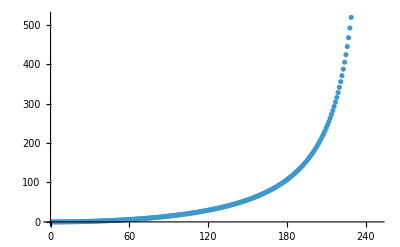

```mathematica
ListPlot[
	Table[
		(cZ Z)/(1-Z)/.params//N,
		{Z,points}
	]
]
```

Solve PDE using NDSolve with appropriate boundary conditions

```mathematica
sol=NDSolve[
{pde==0/.params//Simplify,
v[0,Z]==0,
	v[1,Z]==0,
	v[P,1]==0
},
v,
{P,Z}∈mesh
]
```

{{v→InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]}}

## 4. Check Compactified Solution

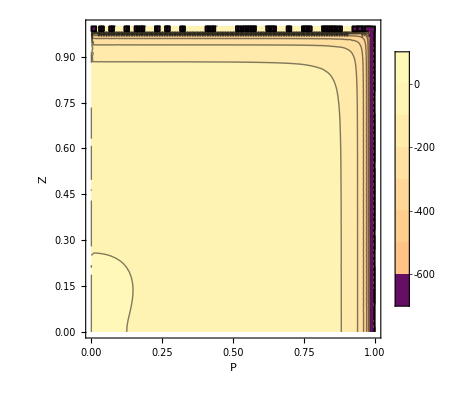

```mathematica
ContourPlot[
v[P,Z]/.sol[[1]],
{P,0,1},
{Z,-1,1},
PlotRange->All,
AxesLabel->Automatic,
PlotLegends->Automatic
]
```

Check boundary conditions and behavior along the axis

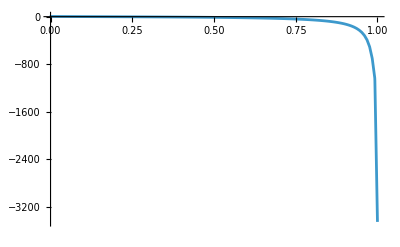

```mathematica
Plot[
v[P,Z]/.sol[[1]]/.Z->0.1,
{P,0,1},
PlotRange->All
]
```

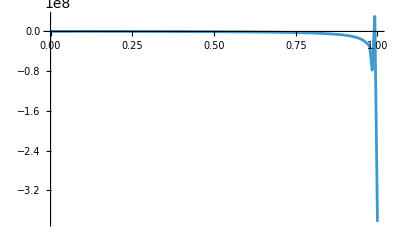

```mathematica
Plot[
D[(v[P,Z]/.sol[[1]]), P]/.P->0,
{Z,0,1},
PlotRange->All
]
```

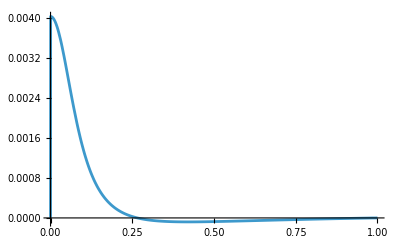

```mathematica
Plot[
D[(v[P,Z]/.sol[[1]]), Z]/.Z->0,
{P,0,1},
PlotRange->All
]
```

## 5. Check Uncompactified Solution

The solution in un-compactified coordinates is

```mathematica
solv[ρ_,z_]=v[ρ/(cP+ρ),z/(cZ+z)]/.sol[[1]];
```

```mathematica
pde2=Laplacian[
solv[ρ,z]/(r1 r2),
{ρ,φ,z},
"Cylindrical"
]-ρ^2/(r1^3 r2^3)/.params//Simplify;
```

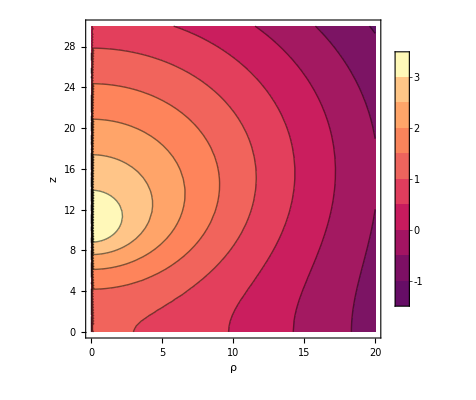

```mathematica
ContourPlot[
solv[ρ,z]/.params,
{ρ,0,20},
{z,0,30},
PlotRange->All,
AxesLabel->Automatic,
PlotLegends->Automatic
]
```

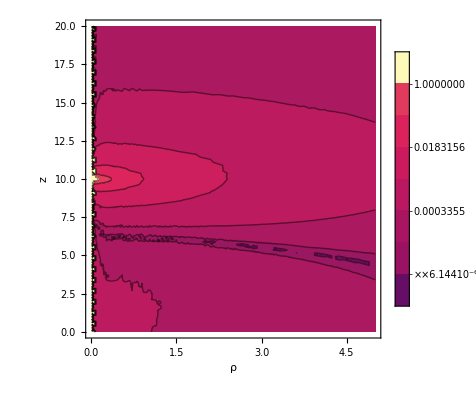

```mathematica
ContourPlot[
Abs[pde2],
{ρ,0,5},
{z,0,20},
PlotRange->All,
AxesLabel->Automatic,
PlotLegends->Automatic,
ScalingFunctions->{None,None,"Log"}
]
```

## 6. Export to CSV

Create a matrix where the top row is the Z-axis and the left column in the P-axis

```mathematica
Table[
Chop[u[P,Z]/.sol[[1]]//N,10^-14],
{P,points},
{Z,points}
]
```

```mathematica
Prepend[«,points//N]
```

```mathematica
Transpose[
Prepend[
Transpose[«],
Join[{"P\\Z"},points//N]
]
]
```

```mathematica
Export[
"solution.csv",
«,
"CSV",
"TextDelimiters"->None
]
```

solution.csv

## A. Sketches

```mathematica
AnnotationKeys[u/.sol[[1]]]
```

{Coordinates,DerivativeOrder,Domain,ElementMesh,Evaluate,GetPolynomial,Grid,IndexedElementEvaluate,InterpolationMethod,InterpolationOrder,MethodInformation,Methods,OutputDimensions,ParameterAddress,Periodicity,PlottableQ,Properties,QuantityUnits,Region,Unpack,ValuesOnGrid,VectorEvaluate}

```mathematica
AnnotationValue[u/.sol[[1]],"ValuesOnGrid"]
```

{-0.263015,-0.263015,-0.263015,-0.263006,-0.262854,-0.261478,-0.252991,-0.217905,-0.131775,0.,-0.263014,-0.263014,-0.263015,-0.263006,-0.262853,-0.261477,-0.252988,-0.217901,-0.131775,0.,-0.263013,-0.263013,-0.263014,-0.263005,-0.262851,-0.261467,-0.252951,-0.217849,-0.131768,0.,-0.263009,-0.263009,-0.263008,-0.262998,-0.262839,-0.261417,-0.252763,-0.217587,-0.131734,0.,-0.262971,-0.262972,-0.262981,-0.262983,-0.262796,-0.261234,-0.252089,-0.216687,-0.131618,0.,-0.262993,-0.26299,-0.26295,-0.262872,-0.262666,-0.260585,-0.249812,-0.214006,-0.131264,0.,-0.263853,-0.26386,-0.263965,-0.263887,-0.262067,-0.25603,-0.241023,-0.206274,-0.130156,0.,-0.217044,-0.217042,-0.216996,-0.216753,-0.215892,-0.213199,-0.205333,-0.183605,-0.126057,0.,-0.120787,-0.120787,-0.120788,-0.12079,-0.120798,-0.120826,-0.120782,-0.119364,-0.106727,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

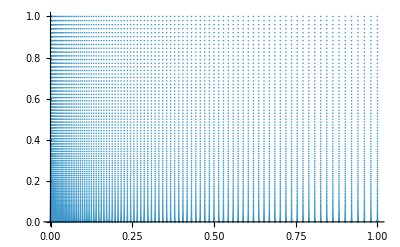

```mathematica
ListPlot[
AnnotationValue[u/.sol[[1]],"Grid"]
]
```

```mathematica
(*
Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.001,"MeshElementType"->QuadElement}}}
*)

(*
mesh=ToElementMesh[
Rectangle[{0,0},{1,1}],
"MaxCellMeasure"->0.0005,
"MeshOrder"->1,
"MeshElementType"->QuadElement
];
*)
```